```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/make_csv

```mathematica
cmap1=Import["matplotlib_option_d.csv","Data"];
```

```mathematica
crainbow=Import["cubehelix_rainbow_256.csv","Data"]/255.;
```

```mathematica
mplrainbow=Import["MPL_rainbow_BW.csv","Data"];
```

```mathematica
Length@crainbow
```

256

```mathematica
?Rectangle
```

RowBox[{"Rectangle", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] represents an axis-aligned filled rectangle from RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}] to RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}].
RowBox[{"Rectangle", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}], "]"}] corresponds to a unit square with its bottom-left corner at RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}].

```mathematica
colorbar[cmap_]:=Graphics[Table[{RGBColor@@cmap[[ii]],Rectangle[{(ii-1)/Length[cmap],0},{ii/Length[cmap],1}]},{ii,1,Length[cmap]}],AspectRatio->0.2]
```

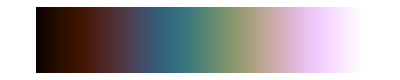

```mathematica
colorbar[crainbow]
```

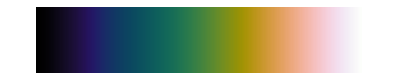

```mathematica
colorbar[mplrainbow]
```

```mathematica
idlcolorbardir="/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values"
idlcolorbarnames=FileNames[idlcolorbardir<>"/*"];
SortBy[idlcolorbarnames,""];
idlcolorbars=If[Mean[Mean[#]]>1,#/255.,#]&/@(Import[#,"CSV"]&/@idlcolorbarnames);
```

/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values

```mathematica
?ReplacePart
```

RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{StyleBox["i", "TI"], "→", StyleBox["new", "TI"]}]}], "]"}] yields an expression in which the StyleBox[RowBox[{StyleBox["i", "TI"], ""}]]SuperscriptBox["", "th"] part of StyleBox["expr", "TI"] is replaced by StyleBox["new", "TI"]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], "→", SubscriptBox[StyleBox["new", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], "→", SubscriptBox[StyleBox["new", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] replaces parts at positions SubscriptBox[StyleBox["i", "TI"], StyleBox["n", "TI"]] by SubscriptBox[StyleBox["new", "TI"], StyleBox["n", "TI"]]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}], "→", StyleBox["new", "TI"]}]}], "]"}] replaces the part at position RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "→", SubscriptBox[StyleBox["new", "TI"], StyleBox["1", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] replaces parts at positions RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["n", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["n", "TI"]], ",", StyleBox["…", "TR"]}], "}"}] by SubscriptBox[StyleBox["new", "TI"], StyleBox["n", "TI"]]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "→", StyleBox["new", "TI"]}]}], "]"}] replaces all parts at positions RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["n", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["n", "TI"]], ",", StyleBox["…", "TR"]}], "}"}] by StyleBox["new", "TI"]. 
RowBox[{"ReplacePart", "[", StyleBox[RowBox[{"i", StyleBox["→", FontSlant -> "Plain"], "new"}], "TI"], "]"}] represents an operator form of ReplacePart that can be applied to an expression.

```mathematica
Position[idlcolorbars,x_/;x>1]
```

{{82,256,1},{83,256,1},{84,256,1},{85,256,1},{86,256,1},{87,256,1},{88,256,1},{89,256,1},{90,256,1},{91,256,1},{92,256,1},{93,256,1}}

```mathematica
idlcolorbars=ReplacePart[idlcolorbars,MapThread[Rule,{Position[idlcolorbars,x_/;x>1],ConstantArray[1,Length[Position[idlcolorbars,x_/;x>1]]]}]]
```

{{{0.,0.,0.},{0.00392157,0.00392157,0.00392157},{0.00784314,0.00784314,0.00784314},{0.0117647,0.0117647,0.0117647},248,{0.988235,0.988235,0.988235},{0.992157,0.992157,0.992157},{0.996078,0.996078,0.996078},{1.,1.,1.}},117,{1}}
 |  |  |  |

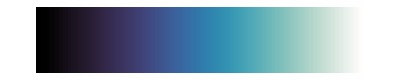

```mathematica
colorbar[idlcolorbars[[-10]]]
```

```mathematica
Export[#1,#2,"CSV"]&@@@({idlcolorbarnames,idlcolorbars}ᵀ)
```

{/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/000_B-W_LINEAR.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/001_BLUE-WHITE.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/002_GRN-RED-BLU-WHT.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/003_RED_TEMPERATURE.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/004_BLUE-GREEN-RED-YELLOW.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/005_STD_GAMMA-II.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/006_PRISM.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/007_RED-PURPLE.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/008_GREEN-WHITE_LINEAR.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/009_GRN-WHT_EXPONENTIAL.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/010_GREEN-PINK.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/011_BLUE-RED.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/012_16_LEVEL.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/013_RAINBOW.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/014_STEPS.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/015_STERN_SPECIAL.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/016_Haze.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/017_Blue_-_Pastel_-_Red.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/018_Pastels.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/019_Hue_Sat_Lightness_1.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/020_Hue_Sat_Lightness_2.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/021_Hue_Sat_Value_1.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/022_Hue_Sat_Value_2.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/023_Purple-Red_plus_Stripes.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/024_Beach.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/025_Mac_Style.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/026_Eos_A.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/027_Eos_B.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/028_Hardcandy.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/029_Nature.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/030_Ocean.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/031_Peppermint.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/032_Plasma.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/033_Blue-Red.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/034_Rainbow.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/035_Blue_Waves.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/036_Volcano.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/037_Waves.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/038_Rainbow18.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/039_Rainbow_plus_white.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/040_Rainbow_plus_black.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/041_CB-Accent.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/042_CB-Dark2.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/043_CB-Paired.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/044_CB-Pastel1.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/045_CB-Pastel2.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/046_CB-Set1.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/047_CB-Set2.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/048_CB-Set3.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/049_CB-Blues.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/050_CB-BuGn.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/051_CB-BuPu.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/052_CB-GnBu.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/053_CB-Greens.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/054_CB-Greys.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/055_CB-Oranges.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/056_CB-OrRd.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/057_CB-PuBu.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/058_CB-PuBuGn.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/059_CB-PuRd.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/060_CB-Purples.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/061_CB-RdPu.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/062_CB-Reds.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/063_CB-YlGn.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/064_CB-YlGnBu.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/065_CB-YlOrBr.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/066_CB-BrBG.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/067_CB-PiYG.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/068_CB-PRGn.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/069_CB-PuOr.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/070_CB-RdBu.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/071_CB-RdGy.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/072_CB-RdYlBu.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/073_CB-RdYlGn.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/074_CB-Spectral.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/075_LAB_rainbow.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/076_MPL_rainbow.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/077_MPL_option_A.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/078_MPL_option_B.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/079_MPL_option_C.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/080_MPL_option_D.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/081_Singlehue_Red.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/082_Singlehue_RedOrange.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/083_Singlehue_Orange.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/084_Singlehue_Gold.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/085_Singlehue_YellowGreen.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/086_Singlehue_Green.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/087_Singlehue_GreenBlue.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/088_Singlehue_Teal.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/089_Singlehue_Blue.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/090_Singlehue_DarkBlue.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/091_Singlehue_Purple.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/092_Singlehue_Indigo.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/093_Multihue_Red1.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/094_Multihue_Red2.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/095_Multihue_Red3.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/096_Multihue_Red4.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/097_Multihue_Red5.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/098_Multihue_Red6.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/099_Multihue_Green1.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/100_Multihue_Green2.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/101_Multihue_Green3.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/102_Multihue_Green4.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/103_Multihue_Green5.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/104_Multihue_Green6.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/105_Multihue_Blue1.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/106_Multihue_Blue2.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/107_Multihue_Blue3.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/108_Multihue_Blue4.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/109_Multihue_Blue5.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/110_Multihue_Blue6.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/111_Multihue_Purple1.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/112_Multihue_Purple2.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/113_Multihue_Purple3.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/114_Multihue_Purple4.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/115_Multihue_Purple5.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/116_Multihue_Purple6.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/117_cyclic1.dat,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_rgb_values/118_cyclic2.dat}

```mathematica
?FileBaseName
```

RowBox[{"FileBaseName", "[", StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] gives the base name for a file without its extension.

```mathematica
FileBaseName[idlcolorbarnames[[1]]]
```

000_B-W_LINEAR

## Now write the python code for viscm

```mathematica
top="from matplotlib.colors import LinearSegmentedColormap
from numpy import nan, inf
";
```

```mathematica
bottom="

test_cm = LinearSegmentedColormap.from_list(__file__, cm_data)


if __name__ == \"__main__\":
    import matplotlib.pyplot as plt
    import numpy as np

    try:
        from pycam02ucs.cm.viscm import viscm
        viscm(test_cm)
    except ImportError:
        print(\"pycam02ucs not found, falling back on simple display\")
        plt.imshow(np.linspace(0, 100, 256)[None, :], aspect='auto',
                   cmap=test_cm)
    plt.show()
";
```

```mathematica
midstrings="cm_data = "<>StringReplace[ToString[#],{"}, {"->"],\n[","{{"->"[[","}}"->"]]"}]&/@idlcolorbars;
```

```mathematica
pyscripts=top<>#<>bottom&/@midstrings;
```

```mathematica
pytestdir="/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/";
```

```mathematica
pyscriptname=pytestdir<>#<>".py"&/@(FileBaseName/@idlcolorbarnames)
```

{/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/000_B-W_LINEAR.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/001_BLUE-WHITE.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/002_GRN-RED-BLU-WHT.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/003_RED_TEMPERATURE.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/004_BLUE-GREEN-RED-YELLOW.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/005_STD_GAMMA-II.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/006_PRISM.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/007_RED-PURPLE.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/008_GREEN-WHITE_LINEAR.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/009_GRN-WHT_EXPONENTIAL.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/010_GREEN-PINK.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/011_BLUE-RED.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/012_16_LEVEL.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/013_RAINBOW.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/014_STEPS.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/015_STERN_SPECIAL.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/016_Haze.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/017_Blue_-_Pastel_-_Red.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/018_Pastels.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/019_Hue_Sat_Lightness_1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/020_Hue_Sat_Lightness_2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/021_Hue_Sat_Value_1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/022_Hue_Sat_Value_2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/023_Purple-Red_plus_Stripes.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/024_Beach.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/025_Mac_Style.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/026_Eos_A.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/027_Eos_B.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/028_Hardcandy.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/029_Nature.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/030_Ocean.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/031_Peppermint.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/032_Plasma.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/033_Blue-Red.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/034_Rainbow.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/035_Blue_Waves.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/036_Volcano.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/037_Waves.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/038_Rainbow18.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/039_Rainbow_plus_white.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/040_Rainbow_plus_black.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/041_CB-Accent.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/042_CB-Dark2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/043_CB-Paired.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/044_CB-Pastel1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/045_CB-Pastel2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/046_CB-Set1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/047_CB-Set2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/048_CB-Set3.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/049_CB-Blues.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/050_CB-BuGn.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/051_CB-BuPu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/052_CB-GnBu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/053_CB-Greens.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/054_CB-Greys.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/055_CB-Oranges.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/056_CB-OrRd.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/057_CB-PuBu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/058_CB-PuBuGn.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/059_CB-PuRd.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/060_CB-Purples.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/061_CB-RdPu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/062_CB-Reds.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/063_CB-YlGn.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/064_CB-YlGnBu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/065_CB-YlOrBr.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/066_CB-BrBG.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/067_CB-PiYG.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/068_CB-PRGn.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/069_CB-PuOr.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/070_CB-RdBu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/071_CB-RdGy.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/072_CB-RdYlBu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/073_CB-RdYlGn.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/074_CB-Spectral.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/075_LAB_rainbow.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/076_MPL_rainbow.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/077_MPL_option_A.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/078_MPL_option_B.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/079_MPL_option_C.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/080_MPL_option_D.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/081_Singlehue_Red.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/082_Singlehue_RedOrange.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/083_Singlehue_Orange.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/084_Singlehue_Gold.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/085_Singlehue_YellowGreen.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/086_Singlehue_Green.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/087_Singlehue_GreenBlue.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/088_Singlehue_Teal.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/089_Singlehue_Blue.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/090_Singlehue_DarkBlue.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/091_Singlehue_Purple.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/092_Singlehue_Indigo.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/093_Multihue_Red1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/094_Multihue_Red2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/095_Multihue_Red3.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/096_Multihue_Red4.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/097_Multihue_Red5.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/098_Multihue_Red6.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/099_Multihue_Green1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/100_Multihue_Green2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/101_Multihue_Green3.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/102_Multihue_Green4.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/103_Multihue_Green5.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/104_Multihue_Green6.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/105_Multihue_Blue1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/106_Multihue_Blue2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/107_Multihue_Blue3.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/108_Multihue_Blue4.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/109_Multihue_Blue5.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/110_Multihue_Blue6.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/111_Multihue_Purple1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/112_Multihue_Purple2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/113_Multihue_Purple3.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/114_Multihue_Purple4.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/115_Multihue_Purple5.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/116_Multihue_Purple6.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/117_cyclic1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/118_cyclic2.py}

```mathematica
Do[Export[pyscriptname[[ii]],pyscripts[[ii]],"Text"],{ii,1,Length[pyscripts]}]
```

## Now run the python script to generate pngs for these colormaps

```mathematica
idlpngdir="/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/"
```

/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/

```mathematica
pypngcmds=
Table["python -m viscm show "<>pyscriptname[[ii]]<>" --save "<>idlpngdir<>FileBaseName[idlcolorbarnames[[ii]]]<>".png"<>" --quit",{ii,1,idlcolorbarnames//Length}];
```

```mathematica
?RunProcess
```

RowBox[{"RunProcess", "[", StyleBox["\"\!\(\*StyleBox[\"command\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] runs the specified external command, returning information on the outcome.
RowBox[{"RunProcess", "[", RowBox[{"{", RowBox[{StyleBox["\"\!\(\*StyleBox[\"command\",\"TI\"]\)\"", ShowStringCharacters->True], ",", SubscriptBox[StyleBox["arg", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["arg", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] runs the specified command, with command-line arguments SubscriptBox[StyleBox["arg", "TI"], StyleBox["i", "TI"]].
RowBox[{"RunProcess", "[", RowBox[{StyleBox["command", "TI"], ",", StyleBox["\"\!\(\*StyleBox[\"prop\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] returns only the specified property.
RowBox[{"RunProcess", "[", RowBox[{StyleBox["command", "TI"], ",", StyleBox["prop", "TI"], ",", StyleBox["input", "TI"]}], "]"}] feeds the specified initial input to the command.

```mathematica
pypngcmds[[1]]
```

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/000_B-W_LINEAR.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/000_B-W_LINEAR.png --quit

```mathematica
bashproc=StartProcess["/bin/bash"]
```

ProcessObject[0]

```mathematica
pypngcmds[[1]]
```

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/000_B-W_LINEAR.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/000_B-W_LINEAR.png --quit

```mathematica
StringJoin[Riffle[pypngcmds,"\n\n"]]
```

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/000_B-W_LINEAR.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/000_B-W_LINEAR.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/001_BLUE-WHITE.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/001_BLUE-WHITE.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/002_GRN-RED-BLU-WHT.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/002_GRN-RED-BLU-WHT.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/003_RED_TEMPERATURE.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/003_RED_TEMPERATURE.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/004_BLUE-GREEN-RED-YELLOW.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/004_BLUE-GREEN-RED-YELLOW.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/005_STD_GAMMA-II.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/005_STD_GAMMA-II.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/006_PRISM.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/006_PRISM.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/007_RED-PURPLE.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/007_RED-PURPLE.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/008_GREEN-WHITE_LINEAR.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/008_GREEN-WHITE_LINEAR.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/009_GRN-WHT_EXPONENTIAL.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/009_GRN-WHT_EXPONENTIAL.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/010_GREEN-PINK.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/010_GREEN-PINK.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/011_BLUE-RED.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/011_BLUE-RED.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/012_16_LEVEL.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/012_16_LEVEL.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/013_RAINBOW.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/013_RAINBOW.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/014_STEPS.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/014_STEPS.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/015_STERN_SPECIAL.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/015_STERN_SPECIAL.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/016_Haze.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/016_Haze.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/017_Blue_-_Pastel_-_Red.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/017_Blue_-_Pastel_-_Red.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/018_Pastels.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/018_Pastels.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/019_Hue_Sat_Lightness_1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/019_Hue_Sat_Lightness_1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/020_Hue_Sat_Lightness_2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/020_Hue_Sat_Lightness_2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/021_Hue_Sat_Value_1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/021_Hue_Sat_Value_1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/022_Hue_Sat_Value_2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/022_Hue_Sat_Value_2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/023_Purple-Red_plus_Stripes.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/023_Purple-Red_plus_Stripes.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/024_Beach.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/024_Beach.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/025_Mac_Style.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/025_Mac_Style.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/026_Eos_A.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/026_Eos_A.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/027_Eos_B.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/027_Eos_B.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/028_Hardcandy.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/028_Hardcandy.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/029_Nature.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/029_Nature.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/030_Ocean.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/030_Ocean.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/031_Peppermint.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/031_Peppermint.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/032_Plasma.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/032_Plasma.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/033_Blue-Red.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/033_Blue-Red.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/034_Rainbow.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/034_Rainbow.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/035_Blue_Waves.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/035_Blue_Waves.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/036_Volcano.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/036_Volcano.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/037_Waves.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/037_Waves.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/038_Rainbow18.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/038_Rainbow18.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/039_Rainbow_plus_white.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/039_Rainbow_plus_white.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/040_Rainbow_plus_black.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/040_Rainbow_plus_black.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/041_CB-Accent.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/041_CB-Accent.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/042_CB-Dark2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/042_CB-Dark2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/043_CB-Paired.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/043_CB-Paired.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/044_CB-Pastel1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/044_CB-Pastel1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/045_CB-Pastel2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/045_CB-Pastel2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/046_CB-Set1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/046_CB-Set1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/047_CB-Set2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/047_CB-Set2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/048_CB-Set3.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/048_CB-Set3.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/049_CB-Blues.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/049_CB-Blues.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/050_CB-BuGn.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/050_CB-BuGn.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/051_CB-BuPu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/051_CB-BuPu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/052_CB-GnBu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/052_CB-GnBu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/053_CB-Greens.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/053_CB-Greens.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/054_CB-Greys.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/054_CB-Greys.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/055_CB-Oranges.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/055_CB-Oranges.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/056_CB-OrRd.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/056_CB-OrRd.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/057_CB-PuBu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/057_CB-PuBu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/058_CB-PuBuGn.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/058_CB-PuBuGn.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/059_CB-PuRd.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/059_CB-PuRd.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/060_CB-Purples.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/060_CB-Purples.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/061_CB-RdPu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/061_CB-RdPu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/062_CB-Reds.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/062_CB-Reds.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/063_CB-YlGn.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/063_CB-YlGn.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/064_CB-YlGnBu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/064_CB-YlGnBu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/065_CB-YlOrBr.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/065_CB-YlOrBr.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/066_CB-BrBG.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/066_CB-BrBG.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/067_CB-PiYG.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/067_CB-PiYG.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/068_CB-PRGn.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/068_CB-PRGn.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/069_CB-PuOr.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/069_CB-PuOr.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/070_CB-RdBu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/070_CB-RdBu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/071_CB-RdGy.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/071_CB-RdGy.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/072_CB-RdYlBu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/072_CB-RdYlBu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/073_CB-RdYlGn.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/073_CB-RdYlGn.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/074_CB-Spectral.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/074_CB-Spectral.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/075_LAB_rainbow.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/075_LAB_rainbow.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/076_MPL_rainbow.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/076_MPL_rainbow.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/077_MPL_option_A.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/077_MPL_option_A.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/078_MPL_option_B.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/078_MPL_option_B.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/079_MPL_option_C.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/079_MPL_option_C.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/080_MPL_option_D.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/080_MPL_option_D.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/081_Singlehue_Red.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/081_Singlehue_Red.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/082_Singlehue_RedOrange.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/082_Singlehue_RedOrange.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/083_Singlehue_Orange.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/083_Singlehue_Orange.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/084_Singlehue_Gold.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/084_Singlehue_Gold.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/085_Singlehue_YellowGreen.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/085_Singlehue_YellowGreen.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/086_Singlehue_Green.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/086_Singlehue_Green.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/087_Singlehue_GreenBlue.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/087_Singlehue_GreenBlue.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/088_Singlehue_Teal.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/088_Singlehue_Teal.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/089_Singlehue_Blue.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/089_Singlehue_Blue.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/090_Singlehue_DarkBlue.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/090_Singlehue_DarkBlue.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/091_Singlehue_Purple.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/091_Singlehue_Purple.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/092_Singlehue_Indigo.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/092_Singlehue_Indigo.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/093_Multihue_Red1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/093_Multihue_Red1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/094_Multihue_Red2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/094_Multihue_Red2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/095_Multihue_Red3.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/095_Multihue_Red3.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/096_Multihue_Red4.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/096_Multihue_Red4.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/097_Multihue_Red5.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/097_Multihue_Red5.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/098_Multihue_Red6.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/098_Multihue_Red6.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/099_Multihue_Green1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/099_Multihue_Green1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/100_Multihue_Green2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/100_Multihue_Green2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/101_Multihue_Green3.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/101_Multihue_Green3.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/102_Multihue_Green4.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/102_Multihue_Green4.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/103_Multihue_Green5.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/103_Multihue_Green5.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/104_Multihue_Green6.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/104_Multihue_Green6.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/105_Multihue_Blue1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/105_Multihue_Blue1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/106_Multihue_Blue2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/106_Multihue_Blue2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/107_Multihue_Blue3.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/107_Multihue_Blue3.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/108_Multihue_Blue4.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/108_Multihue_Blue4.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/109_Multihue_Blue5.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/109_Multihue_Blue5.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/110_Multihue_Blue6.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/110_Multihue_Blue6.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/111_Multihue_Purple1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/111_Multihue_Purple1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/112_Multihue_Purple2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/112_Multihue_Purple2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/113_Multihue_Purple3.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/113_Multihue_Purple3.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/114_Multihue_Purple4.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/114_Multihue_Purple4.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/115_Multihue_Purple5.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/115_Multihue_Purple5.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/116_Multihue_Purple6.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/116_Multihue_Purple6.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/117_cyclic1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/117_cyclic1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_test/118_cyclic2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/IDL_py_png/118_cyclic2.png --quit

I then copied and pasted the above expression into a terminal, which had the desired effect.